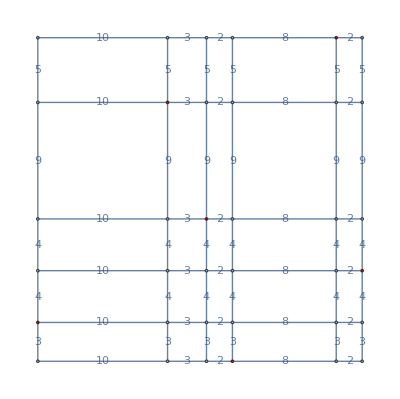

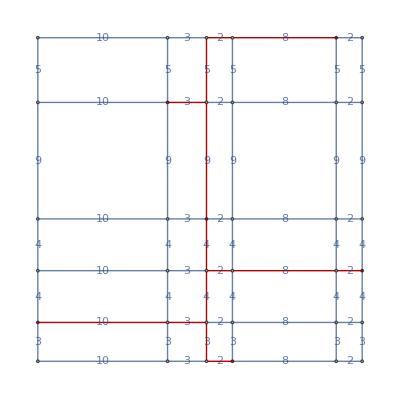
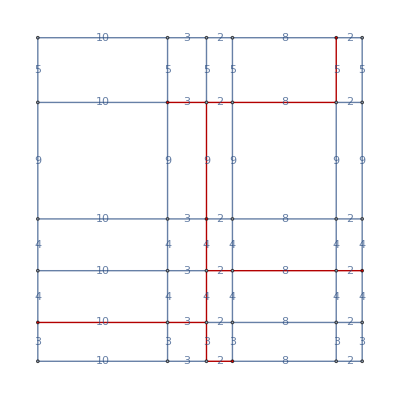
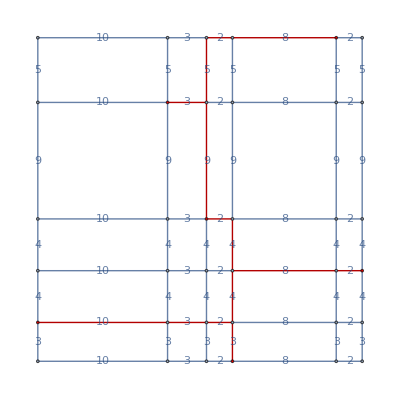
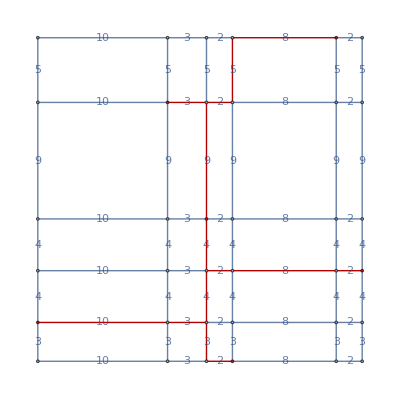
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll["Global`*"]

(*dim gives the dimension of the points*)
dim=2;
(*vert gives the list of dim-dimensional vertices*)
vert ={{20,20},{33,25},{23,11},{35,7},{25,0},{10,3}};
(*{0,15},{5,20},{16,24},{20,20},{33,25},{23,11},{35,7},{25,0},{10,3}*)


(*This function takes a list of dim-dimensional points and returns the hanan grid generated by them.*)
gethanangrid[vertin_]:=Module[{vert=vertin,dict},

(*Create all hanan vertices*)
hananvert = DeleteDuplicates[Distribute[Transpose[vert],List]];

(*Print["Hanan Grid vertices: ",hananvert];*)

hanandat={};

Do[
(*Initialize dictionary stucture with every point in hananvert a key*)
Map[Function[i,dict[d,i]={}],hananvert];
(*Find all (dim-d)-embeded edges*)
Map[Function[i,Map[Function[j,If[Count[MapThread[Equal,{i,j}],False]==1&&i[[d]]≠j[[d]],AppendTo[dict[d,i],j] ]],hananvert]],hananvert];
(*Reduce to adjacent edges only*)
Map[Function[key,
(*Print["dict[",d,",",key,"]: ",dict[d,key]];*)
temp=Sort[Map[Function[val,{key[[d]]-val[[d]],key, val}],dict[d,key]],#1[[1]]<#2[[1]]&];
If[temp[[1,1]]>0,AppendTo[hanandat,{UndirectedEdge[temp[[1,2]],temp[[1,3]]],Abs[temp[[1,1]]]}],
If[temp[[-1,1]]<0,AppendTo[hanandat,{UndirectedEdge[temp[[-1,2]],temp[[-1,3]]],Abs[temp[[-1,1]]]}],
pos = FirstPosition[temp,{x_ /; x>0, _, _},Null,1];
AppendTo[hanandat,{UndirectedEdge[temp[[pos,2]][[1]],temp[[pos,3]][[1]]],Abs[temp[[pos,1]][[1]]]}];
AppendTo[hanandat,{UndirectedEdge[temp[[pos-1,2]][[1]],temp[[pos-1,3]][[1]]],Abs[temp[[pos-1,1]][[1]]]}];
]
]
],Part[DownValues[dict],All,1,1,2]];
,{d,dim}];

edger=UndirectedEdge[p1_,p2_]:>UndirectedEdge[p2,p1];
hanandat = DeleteDuplicates[hanandat, #1[[1]]==(#2[[1]]/.edger)||#1==#2&];

hananedges = ParallelMap[#[[1]]&,hanandat];
hananedgeweights=ParallelMap[#[[2]]&,hanandat];

(*Print[hananedges]*)

If[dim≤3,
hanang=Graph[hananvert,hananedges,VertexCoordinates->hananvert,VertexStyle->Map[#->Red&,vert],EdgeWeight->hananedgeweights,EdgeLabels->"EdgeWeight"],
hanang=Graph[hananvert,hananedges,VertexStyle->Map[#->Red&,vert],EdgeWeight->hananedgeweights]
];

hanang
]


(*This function finds all minimum cost spanning trees of the given vertex list, vertin, on the hanan grid, gridin. The grid, gridin, must contain all vertices of vertin.*)
mintreesonv[vertin_,gridin_]:=Module[{vert=vertin,grid=gridin},
MinimalBy[Parallelize[Select[Subgraph[grid,#]&/@Map[Join[vert,#]&,Subsets[Complement[VertexList[grid],vert]]],TreeGraphQ]],Length[VertexList[#]]&]
]


(*This function unions the list of graphs, graphsin, on the hanan grid, gridin. The grid, gridin, must contain all vertices of the graphs in graphsin.*)
gunongrid[gridin_,graphsin_]:=Module[{grid=gridin,graphs=graphsin},frame=Flatten[Map[Function[graph,nedges=Complement[EdgeList[graph],EdgeList[grid]];Join[Complement[EdgeList[graph],nedges],Flatten[Map[Function[ed,Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsequences[FindShortestPath[grid,ed[[1]],ed[[2]]],{2}]]],nedges],2]]],graphs],1];framegraph=Subgraph[grid,frame];Map[Function[m,PropertyValue[{framegraph,m},EdgeWeight]=PropertyValue[{wholegrid,m},EdgeWeight]],frame];framegraph]


(*Find hanan grid on vert*)
wholegrid=gethanangrid[vert]

(*Assume that one vertex has degree of at least 2 and brute force the resulting grids*)
mintrees = MinimalBy[DeleteDuplicates[Parallelize[Map[gunongrid[wholegrid,{#[[1]],#[[2]]}]&,Flatten[Map[Function[pair,Distribute[{mintreesonv[pair[[1]],gethanangrid[pair[[1]]]],mintreesonv[pair[[2]],gethanangrid[pair[[2]]]]},List]],Flatten[Map[Function[i,vertminusi=Complement[vert,{i}];Map[{Join[#,{i}],Join[Complement[vertminusi,#],{i}]}&,Subsets[vertminusi,{Ceiling[(Length[vertminusi])/2]}]]],vert],1]],1]]]],ConstantArray[1,VertexCount[#]].WeightedAdjacencyMatrix[#].ConstantArray[1,VertexCount[#]]&];


Parallelize[Map[HighlightGraph[wholegrid,{#}]&,mintrees]]

(*AbsoluteTiming[mintrees]*)
(*AbsoluteTiming[mintreesonv[vert,wholegrid]]*)

(*Parallelize[Map[HighlightGraph[wholegrid,{#}]&,mintreesonv[vert,wholegrid]]]*)
(*Parallelize[Map[HighlightGraph[wholegrid,{#}]&,mintrees]]*)
```